```mathematica
SetOptions[EvaluationNotebook[],CellContext->Notebook]
SetDirectory[FileNameJoin@{ParentDirectory[NotebookDirectory[]],"Shared"}];
Needs["gUtils`"];
Needs["gBRDF`"];
Needs["sgCommon`"];
Needs["gPlots`"];
Needs["gPlots3D`"];
Needs["gSphericalCap`"];
Needs["gPlots3DEx`"];
Needs["gBlochSphere`"];
ResetDirectory[];


Simplify[Integrate[2*2π r R/Sqrt[R^2-r^2],{r,0,R}],Assumptions->R>0]
```

4 π R^2

```mathematica
Simplify[Integrate[2π r R/Sqrt[R^2-r^2],{r,ⅇ,2ⅇ}],Assumptions->{R>0 && 0≤A2≤R}]
(*Simplify[Integrate[2π  R/Sqrt[u],{u,3,5}],Assumptions->{R>0 && 0≤A2≤R}]*)
```

2 π R (-√(-4 ⅇ^2+R^2)+√(-ⅇ^2+R^2))

```mathematica
(-2π R Sqrt[R^2-r^2]/.{r->R})-(-2π R Sqrt[R^2-r^2]/.{r->0})
```

2 π R √(R^2)

```mathematica
(-2π R Sqrt[R^2-r^2]/.{r->A1})-(-2π R Sqrt[R^2-r^2]/.{r->A2})
```

-2 π R √(-A1^2+R^2)+2 π R √(-A2^2+R^2)

```mathematica
D[Sqrt[R^2-u],u]
```

-1/(2 √(R^2-u))

Integrate::argmu: Integrate called with 1 argument; 2 or more arguments are expected.

Integrate[(2 π r R)/u]

```mathematica
Integrate[ r R/Sqrt[R^2-r^2],{r,ⅇ,2ⅇ}]
```

R (-√(-4 ⅇ^2+R^2)+√(-ⅇ^2+R^2))

```mathematica
R (-√(-ArcTan[d1]^2+R^2)+√(-ArcTan[d2]^2+R^2))//FullSimplify
```

R (-√(R^2-ArcTan[d1]^2)+√(R^2-ArcTan[d2]^2))

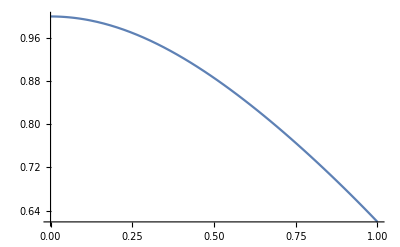

```mathematica
Plot[√(1-ArcTan[d1]^2),{d1,0,1}]
```

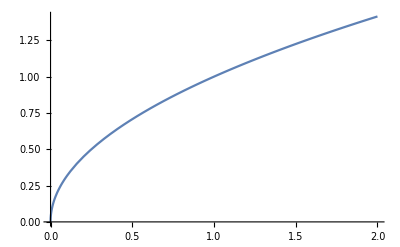

```mathematica
Plot[Sqrt[x],{x,0,2}]
```